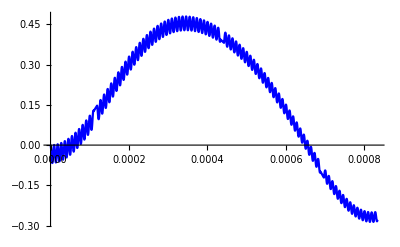

```mathematica
R1=10000;
R2=22000;
R3=33000;
C1=56*10^-9;
C2=47*10^-9;
L=82*10^-6;
uZ[t]=amplitudaU*(Sin[2*Pi*frekvenceU*t])/2;
iZ[t]=amplitudaI*(Sin[2*Pi*frekvenceI*t])/2;

amplitudaU=5;
amplitudaI=100*10^-3;
frekvenceU=1200;
frekvenceI=2400;

uzel1=iU[t]==iR1[t];
uzel2=iR1[t]+iZ[t]==iR2[t]+iC1[t]+iL[t];
uzel3=iL[t]==iZ[t]+iR3[t]+iC2[t];

rovR1=u1[t]-u2[t]==R1*iR1[t];
rovR2=u2[t]==R2*iR2[t];
rovR3=u3[t]==R3*iR3[t];
rovC1=iC1[t]==C1*u2'[t];
rovC2=iC2[t]==C2*u3'[t];
rovL=u2[t]-u3[t]==L*iL'[t];
rovU=u1[t]==uZ[t];

pp1=u2[0]==0;
pp2=u3[0]==0;
pp3=iL[0]==0;

rovnice={uzel1,uzel2,uzel3,rovR1,rovR2,rovR3,rovC1,rovC2,rovL,rovU,pp1,pp2,pp3};
nezname={iU[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],iL[t],u1[t],u2[t],u3[t]};

vysledekU=NDSolve[rovnice,nezname,{t, 0,1*frekvenceU^-1}, StartingStepSize->10^-9];

Plot[Evaluate[u3[t]/.vysledekU], {t, 0, 1*frekvenceU^-1}, PlotStyle->{Blue}]
```